## GlobalSwarmConvergenceInCorner Aaron Becker and Daniel Bao, May 30th 2017

## Convergence Rate for particle swarm in a corner

For Daniel:
1. What combos of  (β,δ)  allow for convergence?
	Answer: For intersection, there is a parallelogram formed by the maximum angular error’s vector and the wall vector. This is where β+2δ<π but the convergence rate is too high
	For convergence, the final distance has to be less than the initial distance so the that would be the equilateral triangle formed by the maximum angular error vector and the wall vector. 2δ=β=π/3
	For wall angles greater than π/3, we must have the 1st inequality satisfied (β+2δ<π) but this is just like the first condition where convergence rate is too high
2. What is the rate of convergence?   (distance after move)/(distance before move) * (max distance moved) for this first move
	Answer: I define distance after move as dfin, distance before move to be dinit, and max distance moved to be dmax, I can calculate each one with EuclideanDistance and then calculate rate.
	Note that max distance moved is going to be distance before move so I will just leave that out.
Answer the question: how far must I move to decrease the error by x?
Rephrasing: Given a beta, how much must my delta change to halve the length of the wall(error length)
Answer: Using properties of similar triangles, decreasing the error length(length of wall) is easy to compute.
For changing delta, halving delta will halve the error length
For change the movement, halving the distance moved from the original point to the wall will also halve the potential error length.

```mathematica
Manipulate[Module[{leftpt,vec},
leftpt = {-1,0};
vec = unc;

x=0;y=0;Bx=0;By=0;Rate=0;dinit=0;dfin=0;Cangle=0;Rate=0;
Graphics[{
(*border*)
(*β=π/2-unc;*)
unc=(π-β)/4;
θ=ArcCot[(2+Cos[β])/Sin[β]];
u={-0.5Cos[β],0.5Sin[β]};
v=leftpt;
θ2=VectorAngle[u,v];

Line[{{-1,0},{0,0},{-Cos[β],Sin[β]}}],
(*Markers for halfway error cone points*)
{Green,Line[{{-0.75,0},{0,0},{-0.75Cos[β],0.75Sin[β]}}]},
{Yellow,Line[{{-0.5,0},{0,0},{-0.5Cos[β],0.5Sin[β]}}]},
{Orange,Line[{{-0.25,0},{0,0},{-0.25Cos[β],0.25Sin[β]}}]},
(*initial swarm*)
{Red,Thick,
Line[{leftpt,{0,0}}]},
{Thick,Blue,Arrow[{leftpt,leftpt+{Cos[vec],Sin[vec]}}]},
{Blue,Arrow[{leftpt,leftpt+{Cos[vec-unc],Sin[vec-unc]}}],
Arrow[{leftpt,leftpt+{Cos[vec+unc],Sin[vec+unc]}}],
Circle[{-1,0},1/3,{vec-unc,vec}],
Text["δ",{-1,0}+1/2{Cos[vec-unc/2],Sin[vec-unc/2]}],
Text["δ",{-1,0}+1/2{Cos[vec+unc/2],Sin[vec+unc/2]}]
},
{Thin,Purple,Arrow[{leftpt,{-0.5Cos[β],0.5Sin[β]}}]},
{Thin,Purple,Arrow[{leftpt,leftpt+{Cos[(vec-unc)/2],Sin[(vec-unc)/2]}}],
Arrow[{leftpt,{-0.25Cos[β],0.25Sin[β]}}],
Circle[{-1,0},1/3,{vec-unc,vec}]
},
Text[θ2,{0.25,0.3}],
Text["β",{-0.2,0.1}],
(*draw the collision point*),
Cangle=π-2unc-β;,
Bx=Sin[β]/Sin[Cangle]*Cos[2unc]-1;
By=Sin[β]/Sin[Cangle]*Sin[2unc];
dinit=EuclideanDistance[leftpt,{0,0}];
dfin=EuclideanDistance[{0,0},{Bx,By}];
Rate=dfin/dinit;,
Text[Rate,{-0.5,1.1}],
(*{Yellow,Thin,Arrow[{leftpt,{Bx,By}}]},*)
{Darker[Green], PointSize[Large],Point[{Bx,By}]}
},PlotRange->{{-1.1,1.1},{-.1,1.5}}
,Axes->True,PlotLabel->"Angles and Collision of a Swarm Particle in Corner Aggregation",
AxesLabel->{"x","y"},ImageSize->Large]]
,{{β,π/3},0,π}
(*{{unc,(π-β)/4,"δ"},0,π/3}*)
(*{{vec,π/6},0,2π},*)
]
```

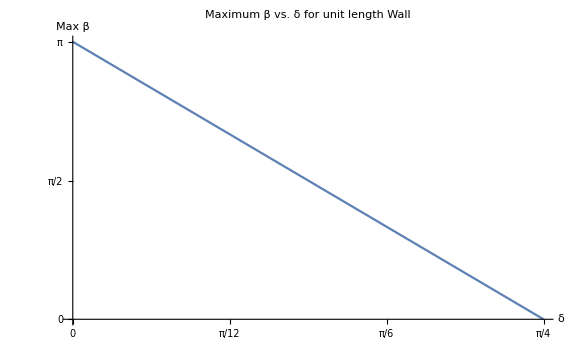

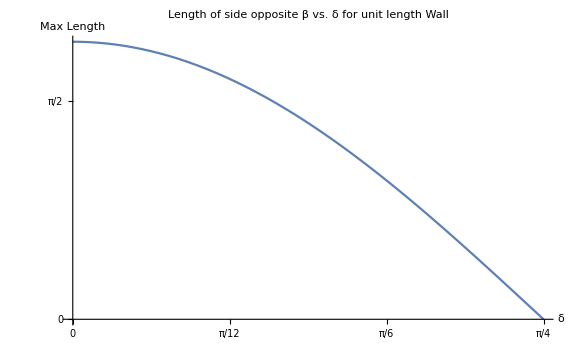

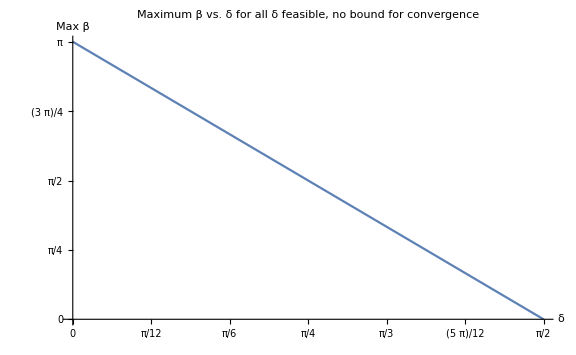

```mathematica
Plot[π-4δ,{δ,0,π/4},PlotLabel->"Maximum β vs. δ for unit length Wall", AxesLabel->{"δ","Max β"},
Ticks->{{0,π/12,π/6,π/4},{0,π/2,π}},ImageSize->Large]
Plot[Sin[π-4δ]/Sin[2δ],{δ,0,π/4},PlotLabel->"Length of side opposite β vs. δ for unit length Wall", AxesLabel->{"δ","Max Length"},
Ticks->{{0,π/12,π/6,π/4,π/3},{0,π/2,π}},ImageSize->Large]
Plot[π-2δ,{δ,0,π/2},PlotLabel->"Maximum β vs. δ for all δ feasible, no bound for convergence",AxesLabel->{"δ","Max β"},
Ticks->{{0,π/12,π/6,π/4,π/3,5π/12,π/2},{0,π/4,π/2,3π/4,π}},ImageSize->Large]
```

```mathematica
Plot3D[{Sin[δ]/Sin[π-β-δ]},{δ,0,π/3},{β,0,π/3},AxesLabel->{"δ","β","Length to corner"},
Ticks->{{0,π/12,π/6,π/4,π/3},{0,π/12,π/6,π/4,π/3},{0,π/8,π/4}},ImageSize->Large]
```

-Graphics3D-